```mathematica
cwdPath=NotebookDirectory[];
outPath=cwdPath<>"out/";
outPath="/home/michal/Documents/inz/results_sig-10_4C/resultset/";

s4K=4*1024;
s512K=512*1024;
s1M=2*s512K;
s4M=4*s1M;
s16M=16*s1M;
s32M=32*s1M;
s64M=64*s1M;
s128M=128*s1M;

gNodes={1,2,3,4,5,6,7,8,9,10};
gSizes={s4K,s512K,s1M,s4M,s16M,s32M,s64M};
gThred={1,2,3,4,5,6,7,8};
gActon={"create","read","update"};

MeanVal[iter_,data_]:={Mean[data],MeanDeviation[data]}/10^6/iter//N;
ParsePhase1[readListResult_]:={#1,#2,MeanVal[#3,#4]}&@@@readListResult;
ParsePhase2[threadsNum_,readListResult_]:=Prepend[#,threadsNum]&/@ParsePhase1[readListResult];
ParsePhase3[action_]:=ParsePhase2[#,ReadList[outPath<>action<>"-"<>ToString[#]<>"n.log"]]&/@gNodes//Flatten[#,1]&;
(*Result:{{nodes,size,threads,{mean,stddev}},...}*)

RawDataCreate=ParsePhase3["create"];
RawDataRead=ParsePhase3["read"];
RawDataUpdate=ParsePhase3["update"];

GetData[collection_,node_,size_,thrd_]:=Cases[collection,{node,size,thrd,_}][[1]][[4]];
GetCreate[node_,size_,thrd_]:=GetData[RawDataCreate,node,size,thrd];
GetRead[node_,size_,thrd_]:=GetData[RawDataRead,node,size,thrd];
GetUpdate[node_,size_,thrd_]:=GetData[RawDataUpdate,node,size,thrd];

GetSeriesInNodes[collection_,nodes_,size_,thrd_]:={#,GetData[collection,#,size,thrd][[1]]}&/@nodes;
GetSeriesInSizes[collection_,node_,sizes_,thrd_]:={#,GetData[collection,node,#,thrd][[1]]}&/@sizes;
GetSeriesInThrds[collection_,node_,size_,thrds_]:={#,GetData[collection,node,size,#][[1]]}&/@thrds;

GetCreateSeriesInNodes[n_,s_,t_]:=GetSeriesInNodes[RawDataCreate,n,s,t];
GetCreateSeriesInSizes[n_,s_,t_]:=GetSeriesInSizes[RawDataCreate,n,s,t];
GetCreateSeriesInThrds[n_,s_,t_]:=GetSeriesInThrds[RawDataCreate,n,s,t];

GetReadSeriesInNodes[n_,s_,t_]:=GetSeriesInNodes[RawDataRead,n,s,t];
GetReadSeriesInSizes[n_,s_,t_]:=GetSeriesInSizes[RawDataRead,n,s,t];
GetReadSeriesInThrds[n_,s_,t_]:=GetSeriesInThrds[RawDataRead,n,s,t];

GetUpdateSeriesInNodes[n_,s_,t_]:=GetSeriesInNodes[RawDataUpdate,n,s,t];
GetUpdateSeriesInSizes[n_,s_,t_]:=GetSeriesInSizes[RawDataUpdate,n,s,t];
GetUpdateSeriesInThrds[n_,s_,t_]:=GetSeriesInThrds[RawDataUpdate,n,s,t];
```

```mathematica
PrettyPlot[series_,plotLabel_,legendLabel_,axesLabel_]:=ListLinePlot[
#2&@@@series,
PlotTheme->"Detailed",
PlotLabel->plotLabel,
Filling->Axis,
AxesOrigin->{0,0},
PlotMarkers->{Automatic,10},
AxesLabel->axesLabel,
LabelStyle->{FontColor->Black,FontSize->15},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AspectRatio->1/GoldenRatio,
InterpolationOrder->None,
PlotLegends->Placed[
LineLegend[
{#1&@@@series},
LegendLabel-> legendLabel
],{0.75,0.75}]
];
```

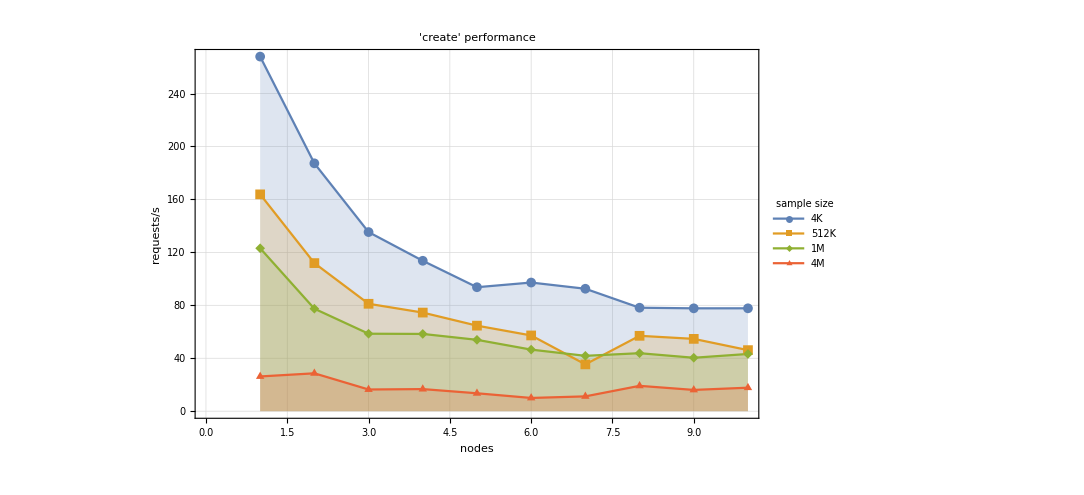

```mathematica
PrettyPlot[
{
{"4K",{#1,1/#2}&@@@GetCreateSeriesInNodes[gNodes,gSizes[[1]],gThred[[4]]]},
{"512K",{#1,1/#2}&@@@GetCreateSeriesInNodes[gNodes,gSizes[[2]],gThred[[4]]]},
{"1M",{#1,1/#2}&@@@GetCreateSeriesInNodes[gNodes,gSizes[[3]],gThred[[4]]]},
{"4M",{#1,1/#2}&@@@GetCreateSeriesInNodes[gNodes,gSizes[[4]],gThred[[4]]]}
},
"'create' performance",
"sample size",
{"nodes","requests/s"}
]
```